# Maps and periodic orbits.

Just a few reminders. A map is a function
	g:ℝ^m→ℝ^m
An orbit of a map with initial condition x_0 is the sequence
	x_0,x_1=g[x_0],…,x_(k+1)=g[x_k],… 
An orbit is periodic if there is a p≥1 satisfying
	x_(k+p)=x_k for all k.
The period of a periodic orbit is the smallest p≥1 that works.

## First Return Maps of ODEs on Sections are Maps

The first return map for the Roseller ODE on the plane y_2==0 is a map on the 2D plane 
	S_2=span((1
0
0),(0
0
1))  
Periodic orbits for the Rosseler ODE with winding number w are periodic maps with period p=w on the plane S_2.

## Rosseller Peak Map

The peak height of the loops on the Rosseler map is a 1D map on the line -∞<x<∞.

```mathematica
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};
CutPlane={Opacity[0.3],Polygon[{{-12,0,0},{12,0,0},{12,0,20},{-12,0,20}}]};
IVP[y0_] := {y'[t]==f[StdParams][y[t]],y[0]==y0};
IVPJ[y0_]:={
y'[t]==f[StdParams][y[t]],y[0]==y0,
J'[t]==df[StdParams][y[t]].J[t],J[0]==IdentityMatrix[3]}
```

Here is the peak height map computation

```mathematica
y0={3.2,8.4,7.6}; TMax=12345; NumPoints=10^3;
yData=ConstantArray[0,{NumPoints,3}]; i=0; tEnd=TMax;
ySol=NDSolveValue[IVP[y0],y,{t,0, TMax},
Method->{"EventLocator", "Event":>y'[t]⟦3⟧==0,"Direction"->-1,
"EventAction":>If[i++<NumPoints,
yData⟦i⟧=y[t],(tEnd=t;"StopIntegration")]}];

ODEPic=ParametricPlot3D[ySol[t],{t,0,tEnd},
PlotRange->All,PlotPoints->10^3,PlotStyle->Thin,ColorFunction->Function[{x,y,z,t},Hue[t]]];
DotPic =ListPointPlot3D[yData,PlotStyle->Black];
TabView[{
"ODE"->ODEPic,
"Peaks"->Show[ODEPic, DotPic],
"z vs i"->ListPlot[yData⟦All,3⟧,PlotRange->All,AxesLabel->{"i","z"}],
"z_(i - 1) vs z_i"->ListPlot[{yData⟦1;;-2,3⟧,yData⟦2;;-1,3⟧}ᵀ,PlotRange->All,AxesLabel->{"z_(i - 1)","z_i"},Prolog->Line[{{0,0},{20,20}}]],
"z_(i - 2) vs z_i"->ListPlot[{yData⟦1;;-3,3⟧,yData⟦3;;-1,3⟧}ᵀ,PlotRange->All,AxesLabel->{"z_(i - 2)","z_i"},Prolog->Line[{{0,0},{20,20}}]]
},4]
```

12345

It turns out the steep hump in the map is fundamental to the complexity of a map!

## Simple 1D Maps: Logistic Map

Lets make the simplest 1D map that looks like our “peak” map.   The scaled quadratic
	g_r[x]=r x (1-x)
r is a parameter and x is the input and output is called the logistic map.  Lets get a feel for what happens to the orbits as we play with r and x_0.

```mathematica
MaxIter=12356;
r=3.55;
x=0.43;
Data=Table[x=r x (1-x),{MaxIter}];
Data=Data⟦2000;;-1⟧;
TabView[{
"i vs x"->ListPlot[Data,PlotRange->All,Joined->False,AxesLabel->{"i","x"},ColorFunction->Function[{i,x},Hue[0.9 i]]],
"x_(i - 1) vs x_i"->ListPlot[{Data⟦1;;-2⟧,Data⟦2;;-1⟧}ᵀ,PlotRange->All,Joined->False,AxesLabel->{"x_(i - 1)","x_i"},ColorFunction->Function[{i,x},Hue[0.9i]],
PlotStyle->PointSize[0.01]]
}]
```

12

Here is a uniform sample of x values going at the same time for different values of r.

```mathematica
n=50;Δx=1.0/(n+1);xs=Range[Δx,1-Δx,Δx];
TabView[
Table[
Data=NestList[r#(1-#)&,xs,32];
r->ListPlot[Dataᵀ,PlotStyle->PointSize[0.008],PlotRange->All,Frame->True,FrameLabel->{"k","x"}],
{r,3.0,4.0,0.05}],4
]
```

123456789101112131415161718192021

It would be nice to see a bunch of different “r” maps evolving at the same time.

```mathematica
n=50;Δx=1.0/(n+1);xs=Range[Δx,1-Δx,Δx];
Steps=6;
Data=Table[
NestList[r#(1-#)&,xs,Steps],
{r,3.0,4.0,0.05}];
Dimensions[Data]
Data=Transpose[Data,{2,1}];
Dimensions[Data]
TabView[Map[ListPlot,Data]]
```

{21,7,50}

{7,21,50}

1234567

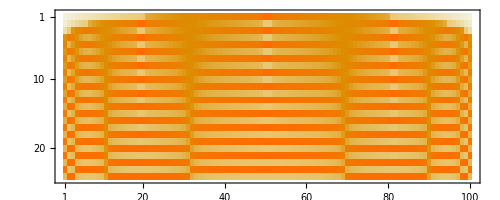

```mathematica
n=100;
xs=RandomReal[{0,1},n];
Δx=1.0/(n+1);xs=Range[Δx,1-Δx,Δx];

x=xs;Table[
x = r x (1-x),
{24}]]
```

One way of doing this is a bifurcation diagram that puts "r" along the bottom and observed "x" values vertically.  You need to make sure that you skip the first few points so that you only see the long term behavior.  You do not want to see the transients.

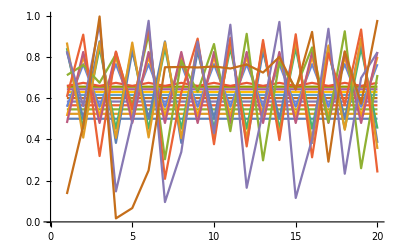

```mathematica
n=10^3;r=3.2;
Data=Table[
x=0.7;
Table[x=r x(1-x),{n}]⟦-20;;-1⟧,
{r,2.,4,0.1}];
ListPlot[Data,Joined->True]
```

## Simple 1D Maps: Tent Map

An even simpler (in some sense) 1D map that looks like our “peak” map is the piecewise linear
	g_μ[x]=μ min(x,1-x)
μ is a parameter and x is the input and output is called the tent map.  Lets get a feel for what happens to the orbits as we play with μ and x_0.

```mathematica
MaxIter=1234;
μ=1.2;
x=0.2;
Data=Table[x=μ Min[x,1-x],{MaxIter}];
TabView[{
"i vs x"->ListPlot[Data,PlotRange->All,Joined->False,AxesLabel->{"i","x"},ColorFunction->Function[{i,x},Hue[0.9 i]]],
"x_(i - 1) vs x_i"->ListPlot[{Data⟦1;;-2⟧,Data⟦2;;-1⟧}ᵀ,PlotRange->All,Joined->False,AxesLabel->{"x_(i - 1)","x_i"},ColorFunction->Function[{i,x},Hue[0.9i]]]
}]
```

12